```mathematica
ClearGlobal[]:=(ClearAll["Global`*"];Clear[Derivative];);
```

```mathematica
ClearGlobal[]
```

```mathematica
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
```

```mathematica
RemoveGlobal[]
```

```mathematica
Good genes for daughters
```

Reproducing Seger-Trivers (1986) paper “Asymmetry in the evolution of female mating preferences”

## Intro

```mathematica
table:= {{"", "T_1","T_2"}, {"Males", "α_1", "α_2"} , {"Females", "β_1", "β_2"}}
```

```mathematica
Grid[table,ItemStyle->{FontFamily->"Latin Modern Roman"}, Alignment->Right]
```

| T_1 | T_2
Males | α_1 | α_2
Females | β_1 | β_2

## Basic Model

### Basic definitions

```mathematica
Subscript[W, 2] := Subscript[t', 2] / Subscript[t, 2]
```

```mathematica
Subscript[W, 1] := Subscript[t', 1] / Subscript[t, 1]
```

```mathematica
Subscript[t, 1] := 1 - Subscript[t, 2]
```

```mathematica
Subscript[p, 1] := 1- Subscript[p, 2]
```

### Frequencies after selection

```mathematica
Subscript[Superscript[t, m], 1] = Subscript[α, 1] Subscript[t, 1] / (Subscript[α, 1] Subscript[t, 1] +Subscript[α, 2] Subscript[t, 2] )
```

((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)

```mathematica
Subscript[Superscript[t, m], 2] = 1- Subscript[Superscript[t, m], 1]
```

1-((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)

```mathematica
Subscript[Superscript[t, f], 1] = Subscript[β, 1] Subscript[t, 1] / (Subscript[β, 1] Subscript[t, 1] +Subscript[β, 2] Subscript[t, 2] )
```

((1-t_2) β_1)/((1-t_2) β_1+t_2 β_2)

```mathematica
Subscript[Superscript[t, f], 2] = 1- Subscript[Superscript[t, f], 1]
```

1-((1-t_2) β_1)/((1-t_2) β_1+t_2 β_2)

### Calculating reproductive success

Reproductive success of T_2 allele(labeled V_2 in the paper):

t'_2=1/2(U_12 p_1+U_22 p_2+(t^f)_2)

Same for T_1 allele (labeled V_1 in the paper):

t'_1=1/2(U_11 p_1+U_21 p_2+(t^f)_1)

Typing this using Superscript[] notation to avoid superscript being interpreted as power:

```mathematica
Subscript[t', 2]:=1/2(Subscript[U, 12]Subscript[p, 1] + Subscript[U, 22]Subscript[p, 2]+Subscript[Superscript[t, f],2])
```

```mathematica
Subscript[t', 1]:=1/2(Subscript[U, 11]Subscript[p, 1] + Subscript[U, 21]Subscript[p, 2]+Subscript[Superscript[t, f],1])
```

## Fixed relative preference

### Female choice

```mathematica
Subscript[U, 22] = Subscript[a, 2]*Subscript[Superscript[t, m], 2]/(Subscript[Superscript[t, m], 1]+Subscript[a, 2]*Subscript[Superscript[t, m], 2])
```

(a_2 (1-((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)))/(((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)+a_2 (1-((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)))

```mathematica
Subscript[U, 11] = Subscript[a, 1]*Subscript[Superscript[t, m], 1]/(Subscript[Superscript[t, m], 2]+Subscript[a, 1]*Subscript[Superscript[t, m], 1])
```

(a_1 (1-t_2) α_1)/(((1-t_2) α_1+t_2 α_2) (1-((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)+(a_1 (1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)))

```mathematica
Subscript[U, 21] := 1-Subscript[U, 22]
```

```mathematica
Subscript[U, 12] := 1-Subscript[U, 11]
```

### Regular plots

```mathematica
sol= FullSimplify[Solve[Subscript[W, 1]==Subscript[W, 2], Subscript[p, 2]]]
```

{{p_2→((-(-1+t_2) α_1+a_2 t_2 α_2) (a_1 α_1 (2 (-1+t_2) β_1+(1-2 t_2) β_2)+α_2 ((1-2 t_2) β_1+2 t_2 β_2)))/((-1+a_1 a_2) α_1 α_2 ((-1+t_2) β_1-t_2 β_2))}}

```mathematica
axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
```

```mathematica
fig1a :=Plot[Evaluate[Subscript[p,2]/.sol /. {Subscript[α, 1] -> 1, Subscript[α, 2] -> 0.6,Subscript[β, 1] -> 1, Subscript[β, 2] -> 1, Subscript[a, 1] -> 1, Subscript[a, 2]->3}], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}]
```

```mathematica
fig1b :=Plot[Evaluate[Subscript[p,2]/.sol /. {Subscript[α, 1] -> 1, Subscript[α, 2] -> 1,Subscript[β, 1] -> 1, Subscript[β, 2] -> 0.6, Subscript[a, 1] -> 1, Subscript[a, 2]->3}], {Subscript[t, 2], 0, 1},PlotStyle->Black, PlotRange->{0,1}, Frame->True, LabelStyle->Black,AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]
```

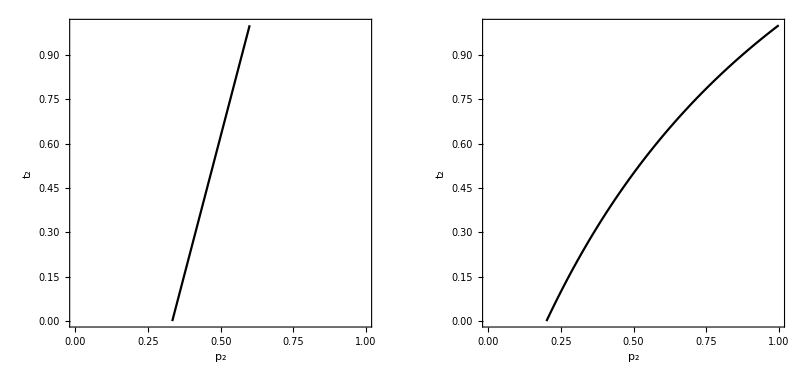

```mathematica
GraphicsRow[{fig1a //axisFlip, fig1b // axisFlip}]
```

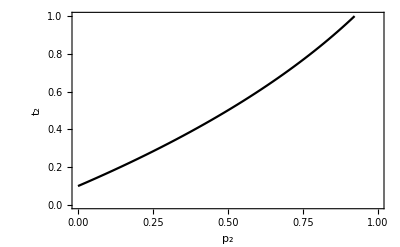

```mathematica
Plot[Evaluate[Subscript[p,2]/.sol /. {Subscript[α, 1] -> 1, Subscript[α, 2] -> .8,Subscript[β, 1] -> 0.8, Subscript[β, 2] -> 1, Subscript[a, 1] -> 1.05, Subscript[a, 2]->1.05}], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, Frame->True, LabelStyle->Black,FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]//axisFlip
```

### Contour plot formula

```mathematica
contourDensityPlot[f_,rx_,ry_,opts:OptionsPattern[]]:=(* //Created by Jens U.Nöckel for Mathematica 8,revised 12/2011*)Module[{img,cont,pL,p,plotRangeRule,densityOptions,contourOptions,frameOptions,rangeCoords},densityOptions=Join[FilterRules[{opts},FilterRules[Options[DensityPlot],Except[{ImageSize,Prolog,Epilog,FrameTicks,PlotLabel,ImagePadding,GridLines,Mesh,AspectRatio,PlotRangePadding,Frame,Axes}]]],{PlotRangePadding->None,ImagePadding->None,Frame->None,Axes->None}];
pL=DensityPlot[f,rx,ry,Evaluate@Apply[Sequence,densityOptions]];
p=First@Cases[{pL},Graphics[__],∞];
plotRangeRule=FilterRules[Quiet@AbsoluteOptions[p],PlotRange];
contourOptions=Join[FilterRules[{opts},FilterRules[Options[ContourPlot],Except[{Prolog,Epilog,FrameTicks,Background,ContourShading,Frame,Axes}]]],{Frame->None,Axes->None,ContourShading->False}];
(* //The density plot img and contour plot cont are created here:*)img=Rasterize[p,"Image"];
cont=If[MemberQ[{0,None},(Contours/.FilterRules[{opts},Contours])],{},ContourPlot[f,rx,ry,Evaluate@Apply[Sequence,contourOptions]]];
(* //Before showing the plots,set the PlotRange for the frame which will be drawn separately:*)frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
(* //To align the image img with the contour plot,enclose img in a bounding box rectangle of the same dimensions as cont,
//and then combine with cont using Show:*)If[Head[pL]===Legended,Legended[#,pL[[2]]],#]&@Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],cont,Evaluate@Apply[Sequence,frameOptions]]]
```

### Contour plots

```mathematica
fig1ax := contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.{Subscript[α, 1] -> 1, Subscript[α, 2] -> 0.6,Subscript[β, 1] -> 1, Subscript[β, 2] -> 1, Subscript[a, 1] -> 1, Subscript[a, 2]->3},{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]
```

```mathematica
fig1bx := contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /. {Subscript[α, 1] -> 1, Subscript[α, 2] -> 1,Subscript[β, 1] -> 1, Subscript[β, 2] -> 0.6, Subscript[a, 1] -> 1, Subscript[a, 2]->3},{Subscript[p, 2],0,1},{Subscript[t, 2],0,1}, ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]
```

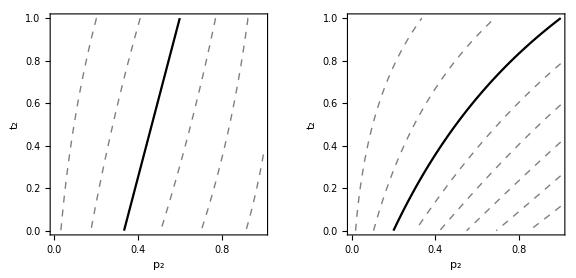

```mathematica
GraphicsRow[{Show[fig1ax, fig1a // axisFlip], Show[fig1bx, fig1b // axisFlip]}, ImageSize->Large]
```

## Best-of-2

### Female choice

```mathematica
Subscript[U, 22] = Subscript[Superscript[t,m], 2] + Subscript[c,2] *Subscript[Superscript[t,m], 1]*Subscript[Superscript[t,m], 2]
```

1-((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)+(c_2 (1-t_2) α_1 (1-((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)))/((1-t_2) α_1+t_2 α_2)

```mathematica
Subscript[U, 11] = Subscript[Superscript[t,m], 1] + Subscript[c,1] *Subscript[Superscript[t,m], 1]*Subscript[Superscript[t,m], 2]
```

((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)+(c_1 (1-t_2) α_1 (1-((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)))/((1-t_2) α_1+t_2 α_2)

### Plots

```mathematica
sol= FullSimplify[Solve[Subscript[W, 1]==Subscript[W, 2], Subscript[p, 2]]]
```

{{p_2→(-(-1+t_2) α_1^2 (2 (-1+t_2) β_1+(1-2 t_2) β_2)+t_2 α_2^2 ((1-2 t_2) β_1+2 t_2 β_2)+α_1 α_2 ((-1+t_2) (-1+c_1+4 t_2) β_1-t_2 (-3+c_1+4 t_2) β_2))/((c_1+c_2) α_1 α_2 ((-1+t_2) β_1-t_2 β_2))}}

```mathematica
args3 := {Subscript[α, 1] -> 1, Subscript[α, 2] ->1,Subscript[β, 1] -> 1, Subscript[β, 2] -> 0.6, Subscript[c, 1] -> 0, Subscript[c, 2]->1}
```

```mathematica
args3old := {Subscript[α, 1] -> 1, Subscript[α, 2] -> 0.6,Subscript[β, 1] -> 1, Subscript[β, 2] -> 1, Subscript[c, 1] -> 0, Subscript[c, 2]->1}
```

```mathematica
fig3bx :=Plot[Evaluate[Subscript[p,2]/.sol /. args3], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}]//axisFlip
```

```mathematica
fig3b:= contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args3,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]
```

```mathematica
fig3ax :=Plot[Evaluate[Subscript[p,2]/.sol /. args3old], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}]//axisFlip
```

```mathematica
fig3a := contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args3old,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]
```

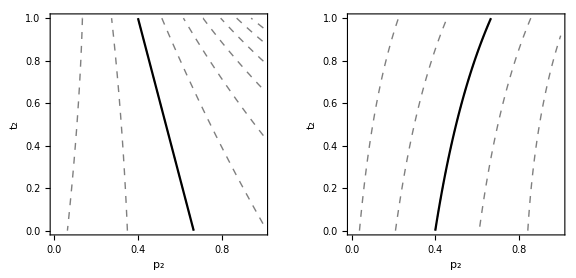

```mathematica
GraphicsRow[{Show[fig3a, fig3ax], Show[fig3b, fig3bx]}, ImageSize->Large]
```

## Best-of-N

### Female choice

```mathematica
Subscript[U, 22] = 1-Subscript[Superscript[t,m], 1]^n
```

1-(((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2))^n

```mathematica
Subscript[U, 11] = Subscript[Superscript[t,m], 1]
```

((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)

### Plots

```mathematica
sol= FullSimplify[Solve[Subscript[W, 1]==Subscript[W, 2], Subscript[p, 2]]]
```

{{p_2→-((-1+t_2) t_2 (α_1 (2 (-1+t_2) β_1+(1-2 t_2) β_2)+α_2 ((1-2 t_2) β_1+2 t_2 β_2)))/((-(-1+t_2) α_1+(-1+t_2) α_1 (((-1+t_2) α_1)/((-1+t_2) α_1-t_2 α_2))^(-1+n)) ((-1+t_2) β_1-t_2 β_2))}}

```mathematica
args3 := {Subscript[α, 1] -> 1, Subscript[α, 2] ->1,Subscript[β, 1] -> 1, Subscript[β, 2] -> 0.6, n-> 3}
```

```mathematica
args3old := {Subscript[α, 1] -> 1, Subscript[α, 2] -> 0.6,Subscript[β, 1] -> 1, Subscript[β, 2] -> 1, n-> 3}
```

```mathematica
fig3bx :=Plot[Evaluate[Subscript[p,2]/.sol /. args3], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}]//axisFlip
```

```mathematica
fig3b:= contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args3,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]
```

```mathematica
fig3ax :=Plot[Evaluate[Subscript[p,2]/.sol /. args3old], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}]//axisFlip
```

```mathematica
fig3a := contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args3old,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]
```

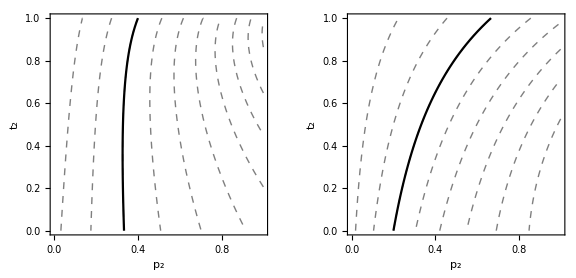

```mathematica
GraphicsRow[{Show[fig3a, fig3ax], Show[fig3b, fig3bx]}, ImageSize->Large]
```